## All of the following is for a Maxwellian

#### Load package

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

```mathematica
(*Limit[LKMwellDensFac[phiBar,RB],RB->∞,Assumptions->phiBar>0]*)
(*1/2 ((2 √phiBar)/(√π)+ⅇ^phiBar Erfc[√phiBar])*)
```

```mathematica
RBs = Reverse@{3,10,30,100,300,1000};
```

## Plot as a function of ϕ̄

```mathematica
kappas={3.55,10.59};
```

```mathematica
plotLKMwellRBFuncs=(LKMwellDensFac[phiBar,#])&/@RBs;
```

```mathematica
plotLKKappaRBFuncs1=(LKKappaDensFac[phiBar,#,kappas[[1]]])&/@RBs;
```

```mathematica
plotLKKappaRBFuncs2=(LKKappaDensFac[phiBar,#,kappas[[2]]])&/@RBs;
```

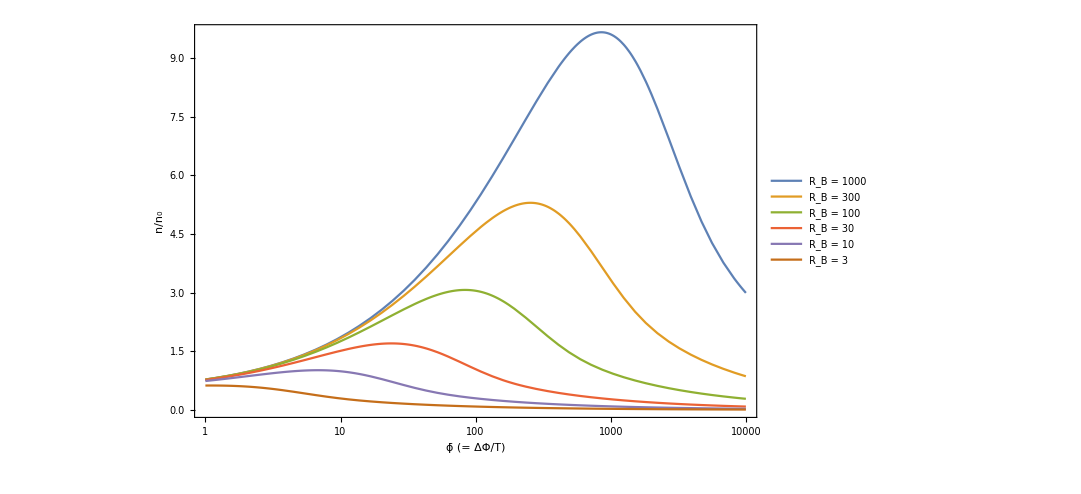

```mathematica
LogLinearPlot[plotLKMwellRBFuncs,{phiBar,1,10000},PlotLegends->((Style[StringForm["R_B = `1`",#],20])&/@RBs),Frame->True,FrameLabel->{"ϕ̄ (= ΔΦ/T)","n/n_0",Style["Liemohn and Khazanov Maxwellian density factor",24]},FrameStyle->(FontSize->20),ImageSize->800]
```

```mathematica
maxMaxwellRBVal[funcNum_]:=(FindMaximum[{plotLKMwellRBFuncs[[funcNum]],2.1<phiBar<1000},{phiBar,3}])[[1]]
```

```mathematica
maxkappaRBVal1[funcNum_]:=(FindMaximum[{plotLKKappaRBFuncs1[[funcNum]],2.1<phiBar<1000},{phiBar,3}])[[1]]
```

```mathematica
maxkappaRBVal2[funcNum_]:=(FindMaximum[{plotLKKappaRBFuncs2[[funcNum]],10<phiBar<1000},{phiBar,10.1}])[[1]]
```

```mathematica
fillTwixt={4,6};
```

```mathematica
maxMaxwellRBVal[fillTwixt[[1]]]
```

1.69996

```mathematica
maxkappaRBVal1[fillTwixt[[1]]]
maxkappaRBVal2[fillTwixt[[1]]]
```

1.59684

1.66733

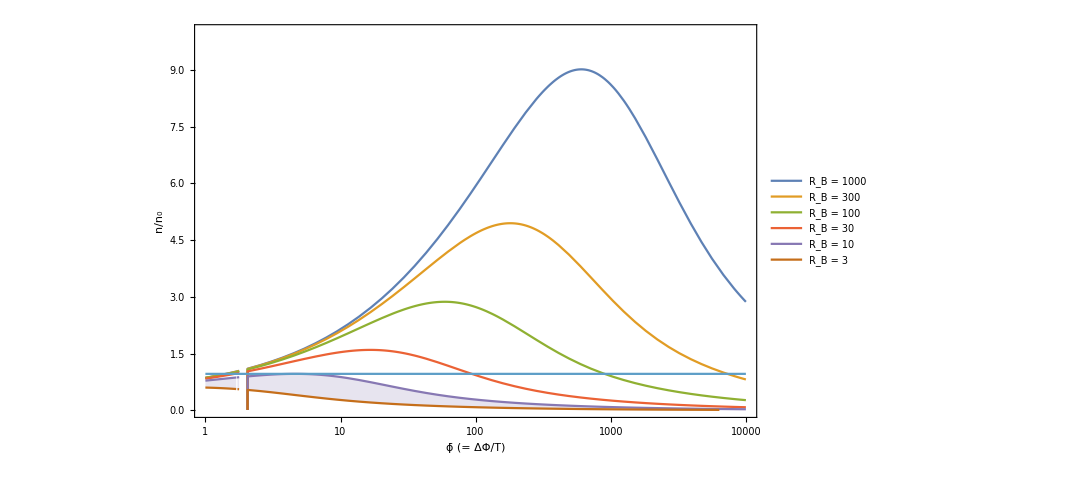

```mathematica
LogLinearPlot[{plotLKKappaRBFuncs1,maxkappaRBVal1[fillTwixt[[1]]]},{phiBar,1,10000},PlotRange->{Automatic,{0.01,10}},Filling->{fillTwixt[[1]]->{fillTwixt[[2]]}},PlotLegends->((Style[StringForm["R_B = `1`",#],20])&/@RBs),Frame->True,FrameLabel->{"ϕ̄ (= ΔΦ/T)","n/n_0",Style[StringForm["Liemohn and Khazanov κ = `1` density factor",kappas[[1]]],24]},FrameStyle->(FontSize->20),ImageSize->800]
```

```mathematica
LogLinearPlot[{plotLKKappaRBFuncs2,maxkappaRBVal2[fillTwixt[[1]]]},{phiBar,1,10000},PlotRange->{Automatic,{0.01,10}},Filling->{fillTwixt[[1]]->{fillTwixt[[2]]}},PlotLegends->((Style[StringForm["R_B = `1`",#],20])&/@RBs),Frame->True,FrameLabel->{"ϕ̄ (= ΔΦ/T)","n/n_0",Style[StringForm["Liemohn and Khazanov κ = `1` density factor",kappas[[2]]],24]},FrameStyle->(FontSize->20),ImageSize->800]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

$Aborted

## Analogous plot, with R_B as main variable

```mathematica
phiBars=RBs;
```

```mathematica
plotLKMWellphiBarFuncs=(LKMwellDensFac[#,RB])&/@phiBars;
```

```mathematica
plotLKKappaphiBarFuncs1=(LKKappaDensFac[#,RB,kappas[[1]]])&/@phiBars;
```

```mathematica
plotLKKappaphiBarFuncs2=(LKKappaDensFac[#,RB,kappas[[2]]])&/@phiBars;
```

```mathematica
fillTwixt={5,6};
```

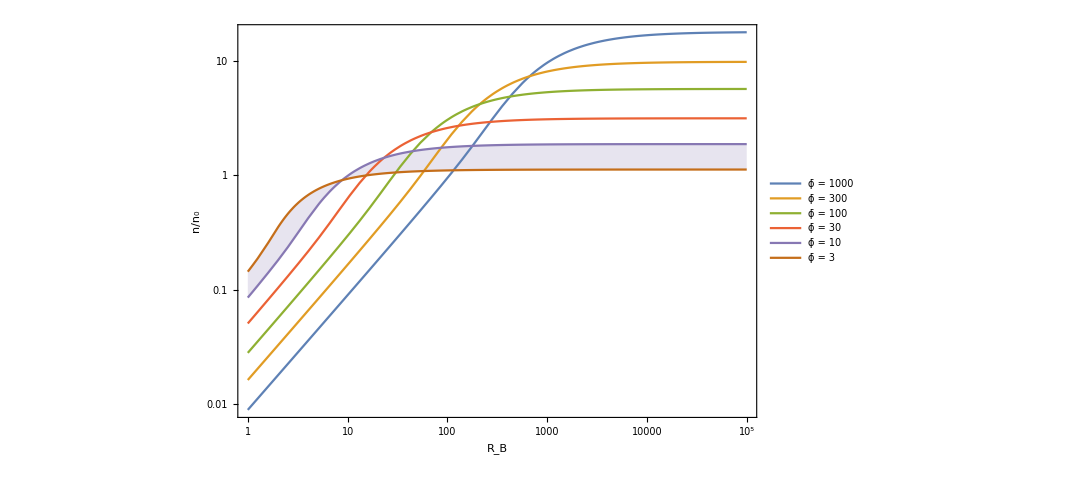

```mathematica
LogLogPlot[plotLKMWellphiBarFuncs,{RB,1,100000},PlotLegends->((Style[StringForm["ϕ̄ = `1`",#],20])&/@phiBars),Filling->{fillTwixt[[1]]->{fillTwixt[[2]]}},Frame->True,FrameLabel->{"R_B","n/n_0",Style["Liemohn and Khazanov Maxwellian density factor",24]},FrameStyle->(FontSize->20),ImageSize->800]
```

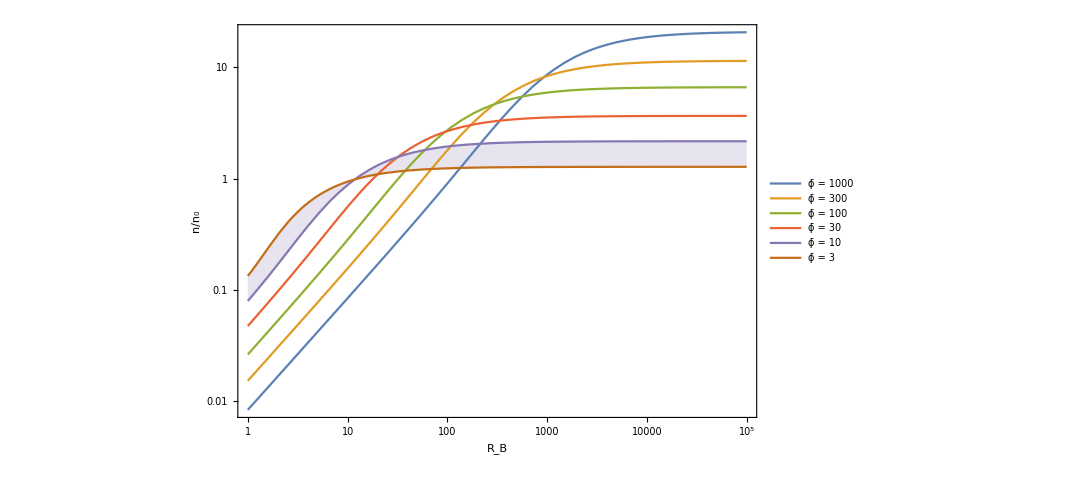

```mathematica
LogLogPlot[plotLKKappaphiBarFuncs1,{RB,1,100000},PlotLegends->((Style[StringForm["ϕ̄ = `1`",#],20])&/@phiBars),Filling->{fillTwixt[[1]]->{fillTwixt[[2]]}},Frame->True,FrameLabel->{"R_B","n/n_0",Style[StringForm["Liemohn and Khazanov κ = `1` density factor",kappas[[1]]],24]},FrameStyle->(FontSize->20),ImageSize->800]
```

## A log-a-tized version of the Liemohn and Khazanov density factor

```mathematica
LKMwellDensFacLogParams[log10phiBar_, log10RB_] :=1/2 ⅇ^(10^log10phiBar) Erfc[√(10^log10phiBar)]+(√(10^log10RB-1) DawsonF[√(10^log10phiBar/(10^log10RB-1))])/(√π)
```

### Now with plots!

```mathematica
Plot3D[Log[LKMwellDensFacLogParams[log10phiBar,log10RB]],{log10phiBar,1,5},{log10RB,1,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[LKMwellDensFacLogParams[log10phiBar,log10RB],{log10phiBar,1,5},{log10RB,1,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
log10phiBars=Log10[phiBars];
```

```mathematica
plotLKMWellLogphiBarFuncs=(LKMwellDensFacLogParams[#,log10RB])&/@log10phiBars;
```

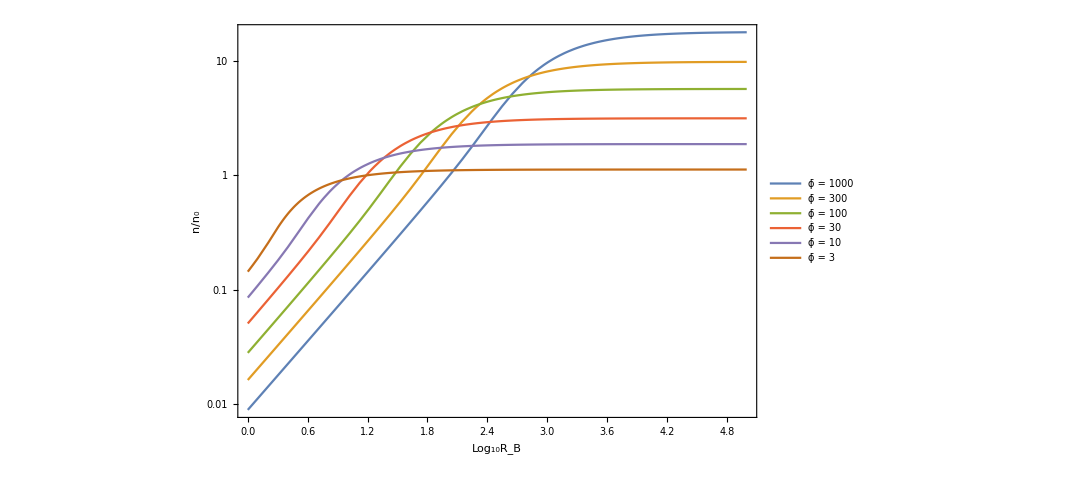

```mathematica
LogPlot[plotLKMWellLogphiBarFuncs,{log10RB,0,5},PlotLegends->((Style[StringForm["ϕ̄ = `1`",#],20])&/@(10^log10phiBars)),Frame->True,FrameLabel->{"Log_10R_B","n/n_0",Style["Liemohn and Khazanov Maxwellian density factor",24]},FrameStyle->(FontSize->20),ImageSize->800]
```

## Orbit 1773-specific plot, with R_B as main variable

```mathematica
phiAboveRange={780,1300};TRange={250,325};
```

```mathematica
phiBars={phiAboveRange[[1]]/TRange[[2]],phiAboveRange[[2]]/TRange[[1]]};
```

```mathematica
phiBars=Reverse@{phiBars[[1]],Mean@phiBars,phiBars[[2]]}
```

{26/5,19/5,12/5}

```mathematica
plotLKMWellphiBarFuncs=(LKMwellDensFac[#,RB])&/@phiBars;
```

```mathematica
minAtLowRB=Min[plotLKMWellphiBarFuncs/.RB->6];
maxAtHighRB=Max[plotLKMWellphiBarFuncs/.RB->11.4];
```

```mathematica
lineStyle={Thick,Red,Dashed};
l1x=1.8;l2x=2.5;
line1=Line[{{l1x,minAtLowRB},{l1x,1.5}}];
line2=Line[{{l2x,0},{l2x,1.5}}];
```

```mathematica
line3=Line[{{l1x,minAtLowRB},{1000,minAtLowRB}}];
line4=Line[{{0,maxAtHighRB},{1000,maxAtHighRB}}];
```

```mathematica
(*Filling->{(Length[plotLKMWellphiBarFuncs]+1)->{(Length[plotLKMWellphiBarFuncs]+2)}},*)
```

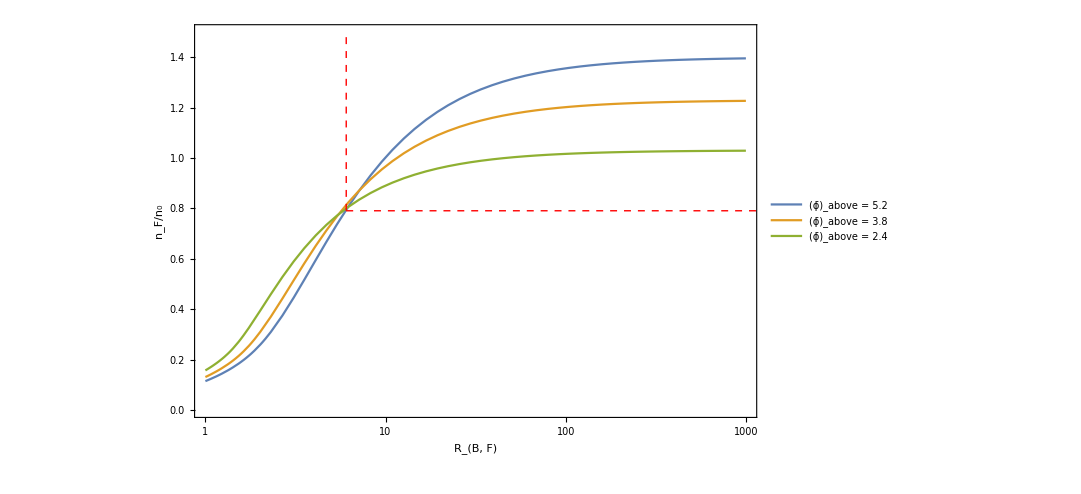

```mathematica
LogLinearPlot[{plotLKMWellphiBarFuncs,line1,line3},{RB,1,1000},PlotRange->{Automatic,{0,1.5}},PlotStyle->Table[Automatic,Length@plotLKMWellphiBarFuncs]~Join~Table[Directive[lineStyle],2],PlotLegends->((Style[StringForm["(ϕ̄)_above = `1`",#//N],20])&/@phiBars),Frame->True,FrameLabel->{"R_(B, F)","n_F/n_0",Style["Liemohn and Khazanov Maxwellian density factor",24]},FrameStyle->(FontSize->20),ImageSize->800,Epilog->{Directive[lineStyle],line1,line3}]
```

```mathematica
plotLKMWellphiBarFuncsScaleIonos=(LKMwellDensFac[#,RB/4])&/@phiBars;
```

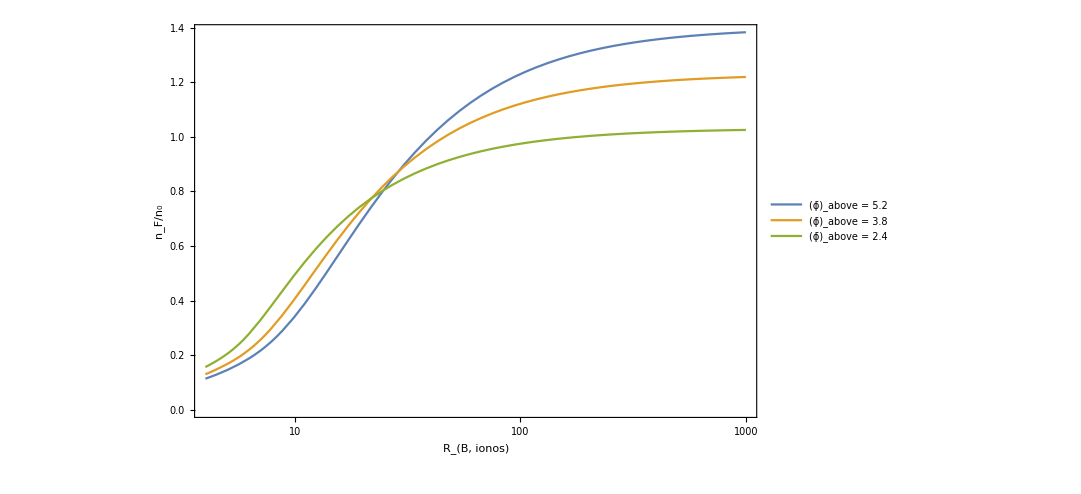

```mathematica
LogLinearPlot[plotLKMWellphiBarFuncsScaleIonos,{RB,4,1000},PlotLegends->((Style[StringForm["(ϕ̄)_above = `1`",#//N],20])&/@phiBars),Frame->True,FrameLabel->{"R_(B, ionos)","n_F/n_0",Style["Liemohn and Khazanov Maxwellian density factor",24]},FrameStyle->(FontSize->20),ImageSize->800]
```

```mathematica
func=(κ-1)/(κ-3/2);
```

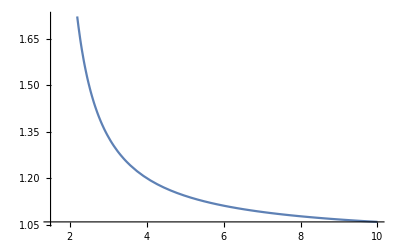

```mathematica
Plot[func,{κ,1.5,10}]
```

```mathematica
func/.κ->3.5//N
```

1.25

```mathematica
jvMaxwellian[pot_,RB_,Tm_,nm_]:=0.0266987 nm Tm^(1/2) RB (1-(1-1/RB)Exp[-(pot/Tm)/(RB-1)])
```

```mathematica
reg1={Tm-> 300,RB-> 4,nm-> 1/2};
```

```mathematica
at1=(jvMaxwellian[pot,RB,Tm,nm]/.reg1)
```

0.92487 (1-(3 ⅇ^(-pot/900))/4)

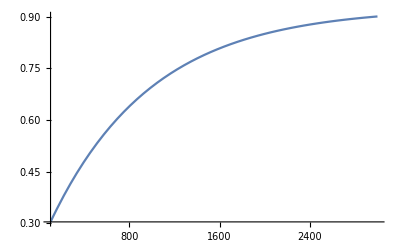

```mathematica
Plot[at1,{pot,100,3000}]
```